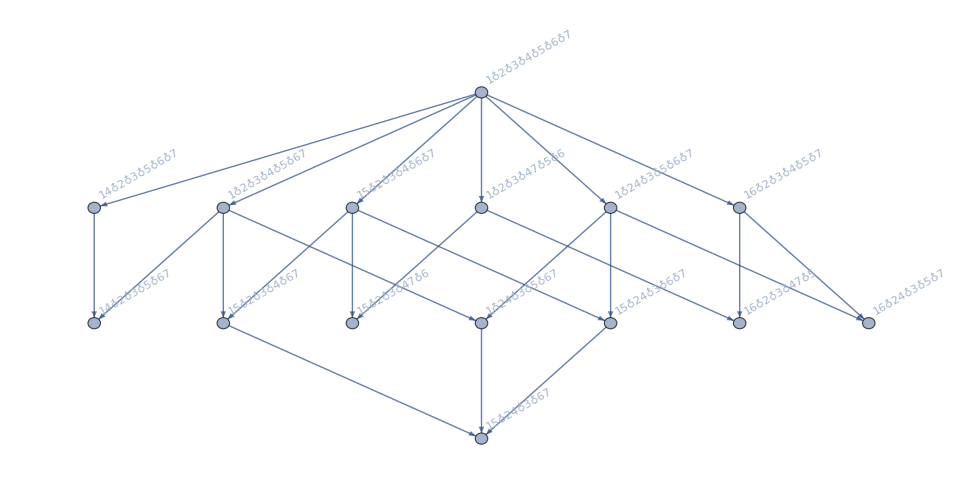

```mathematica
FindFullFormula[ReadGrof[5]]//FormulaGraphReverse2
```

```mathematica
Sort[FindFullFormula[ReadGrof[5]],CompareSymbolsNew]
```

{v1x2x3x4x5x6x7,v14x2x3x5x6x7,v15x2x3x4x6x7,v16x2x3x4x5x7,v1x24x3x5x6x7,v1x2x3x47x5x6,v1x2x3x4x5x67,v14x2x3x5x67,v15x24x3x6x7,v15x2x3x47x6,v15x2x3x4x67,v16x24x3x5x7,v16x2x3x47x5,v1x24x3x5x67,v15x24x3x67}

```mathematica
ZetaFunction[g_]:=Block[{form= FindFullFormula[g], dep, partitions,mat, x, y, trans=Association[],  pos, result},
dep=FormulaGraphReverse2[form];

partitions=Sort[Map[SetsToSymbol, SetPartitions[VertexCount[g]]],CompareSymbols];

pos=1;
Table[trans[sym]=pos;pos++,{sym,partitions}];

result=DiagonalMatrix[Table[0,{k,Length[partitions]}]];
Table[result[[trans[edge[[1]]],trans[edge[[2]]]]]=1,
{edge,EdgeList[dep]}
];
Table[result[[trans[vertex],trans[vertex]]]=1,
{vertex,VertexList[dep]}
];
result=MatrixPower[result,VertexCount[g]];
For[x=1,x<=Length[partitions],x++,
For[y=1,y<=Length[partitions],y++,
If[result[[x,y]]≠0,result[[x,y]]=1,result[[x,y]]=0]
]
];
result
]
```

```mathematica
ZetaFunctionFromFormula[form_]:=Block[{ dep, partitions,mat, x, y, trans=Association[],  pos, result,size},
dep=FormulaGraphReverse2[form];
size=Length[Flatten[SymbolToSets[form[[1]]]]];

partitions=Sort[Map[SetsToSymbol, SetPartitions[size]],CompareSymbols];

pos=1;
Table[trans[sym]=pos;pos++,{sym,partitions}];

result=DiagonalMatrix[Table[0,{k,Length[partitions]}]];
Table[result[[trans[edge[[1]]],trans[edge[[2]]]]]=1,
{edge,EdgeList[dep]}
];
Table[result[[trans[vertex],trans[vertex]]]=1,
{vertex,VertexList[dep]}
];
result=MatrixPower[result,size];
For[x=1,x<=Length[partitions],x++,
For[y=1,y<=Length[partitions],y++,
If[result[[x,y]]≠0,result[[x,y]]=1,result[[x,y]]=0]
]
];
result
]
```

```mathematica
ReadGrof[1]//FindFullFormula
```

{v1x2x3x4}

```mathematica
Map[SymbolToSets,Sort[Map[SetsToSymbol, SetPartitions[3]],CompareSymbolsNew]]
```

{{{1},{2,3}},{{1,2,3}},{{1},{2},{3}},{{1,2},{3}},{{1,3},{2}}}

```mathematica
Clear[v1x23,v123,v1x2x3,v12x3,v13x2]
```

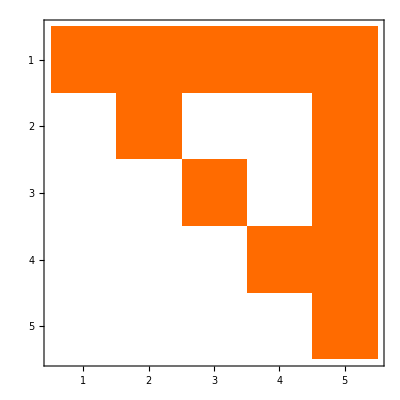

```mathematica
ZetaFunctionFromFormula[{v1x23,v123,v1x2x3,v12x3,v13x2}]//MatrixPlot
```

```mathematica
e3=Graph[Range[3],{}]
```

-Graphics-

```mathematica
FindFullFormula[e3]
```

{v1x2x3,v1x23,v13x2,v12x3,v123}

```mathematica
ZetaFunction[Graph[Range[6],{}]]
```

SparseArray[…]

```mathematica
.
```

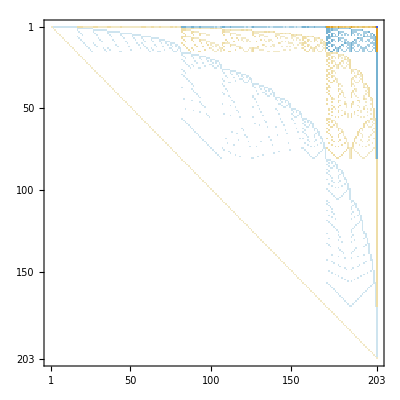

```mathematica
ZetaFunction[Graph[Range[6],{}]]//Inverse//MatrixPlot
```

```mathematica
ZetaFunction[MinimalGraph2[6]]//Total//Total
```

49

```mathematica
ZetaFunction[MinimalGraph[6]]//Total//Total
```

52

```mathematica
ZetaFunction[MinimalGraph[5]]//Total//Total
```

11

```mathematica
ZetaFunction[MinimalGraph2[5]]//Total//Total
```

11

```mathematica
ZetaFunction[MinimalGraph[7]]//Total//Total
```

290

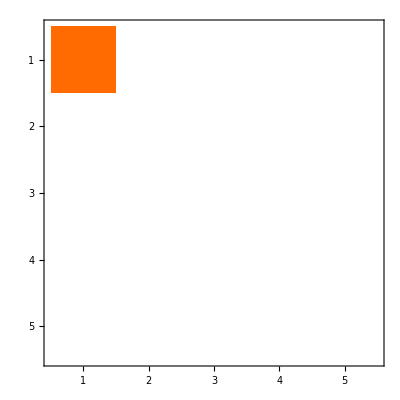

```mathematica
ZetaFunction[CompleteGraph[3]]//MatrixPlot
```

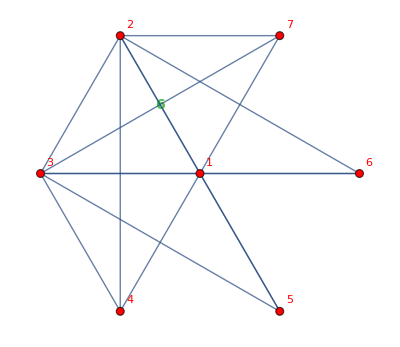
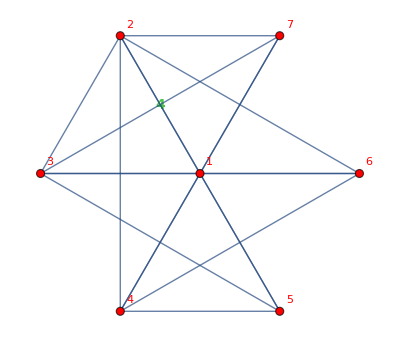
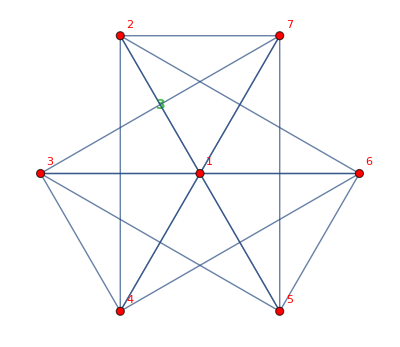

```mathematica
BarelyFourColorableGraphsOfCount[7]
```

```mathematica
Map[MatrixPlot[ZetaFunction[#]]&,BarelyFourColorableGraphsOfCount[8]]
```

$Aborted

```mathematica
DropZeroRow[mat_]:=Select[mat,Total[Abs[#]]≠0&]
```

```mathematica
DropZeroCol[mat_]:=Transpose[Select[Table[mat[[All,k]],{k,Length[mat]}],Total[Abs[#]]≠0&]]
```

```mathematica
DropZeroCol[IdentityMatrix[4]]
```

{{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}}

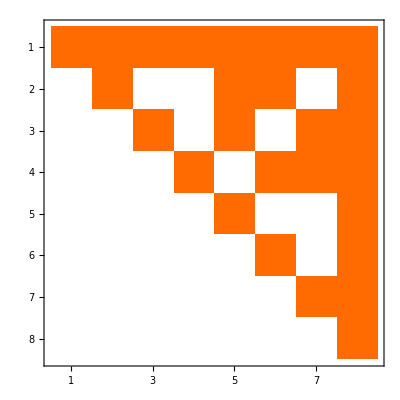

```mathematica
MatrixPlot[DropZeroRow[DropZeroCol[ZetaFunction[-Graphics-]]]]
```

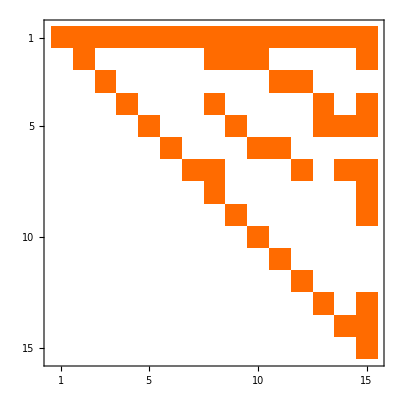

```mathematica
MatrixPlot[DropZeroRow[DropZeroCol[ZetaFunction[MinimalGraph[6]]]]]
```

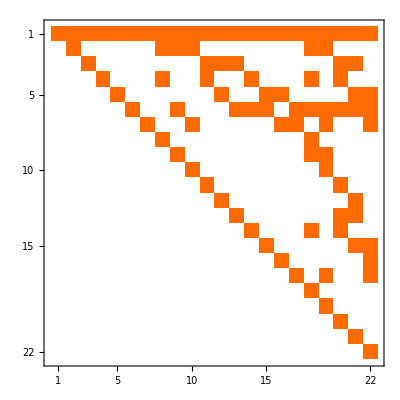

```mathematica
MatrixPlot[DropZeroRow[DropZeroCol[ZetaFunction[JacobsThalGraph[3]]]]]
```

```mathematica
MatrixPlot[DropZeroRow[DropZeroCol[ZetaFunction[JacobsThalGraph[2]]]]]
```

-Graphics-

```mathematica
MatrixPlot[DropZeroRow[DropZeroCol[ZetaFunction[JacobsThalGraph[3]]]]]
```

-Graphics-

{v1x2x3x4x5x67,v1x24x3x5x67,v14x2x3x5x67,v15x2x3x4x67,v15x24x3x67}

{v1x2x3x47x5x6,v16x2x3x47x5,v15x2x3x47x6}

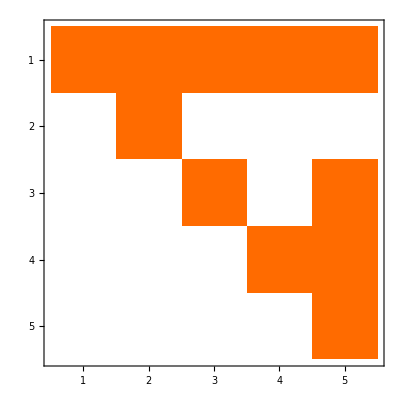
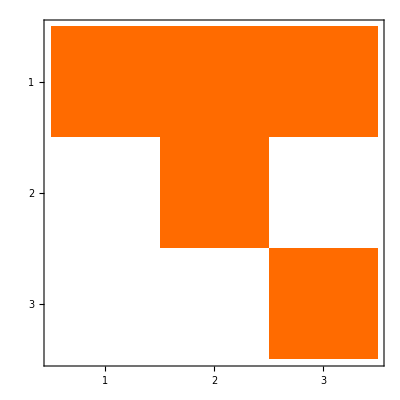
{-Graphics-6<->7,-Graphics-4<->7}

```mathematica
With[{g=ReadGrof[5]},
Monitor[
Table[
With[{form=Map[SymbolReplace[#,e]&,FindFullFormula[GContract[g,e]]]},
Print[form];
Labeled[MatrixPlot[DropZeroRow[DropZeroCol[ZetaFunctionFromFormula[form]]]],e]
],
{e,Map[SortEdge,Take[EdgeList[GraphComplement[g]],-2]]}
],
e]
]
```

```mathematica
With[{g=ReadGrof[3]},
Monitor[
MatrixForm[DropZeroRow[DropZeroCol[Total[
Table[
With[{form=Map[SymbolReplace[#,e]&,FindFullFormula[GContract[g,e]]]},
Print[form];
ZetaFunctionFromFormula[form]
],
{e,Map[SortEdge,EdgeList[GraphComplement[g]]]}

]
]]]
]
,
e]
]
```

{v16x2x3x4x5,v16x24x3x5}

{v14x2x3x5x6}

{v1x24x3x5x6,v16x24x3x5}

(1 | 0 | 0 | 0
0 | 1 | 0 | 1
0 | 0 | 1 | 1
0 | 0 | 0 | 2)

```mathematica
With[{g=ReadGrof[5]},
Monitor[
MatrixForm[DropZeroRow[DropZeroCol[Total[
Table[
With[{form=Map[SymbolReplace[#,e]&,FindFullFormula[GContract[g,e]]]},
Print[form];
ZetaFunctionFromFormula[form]
],
{e,Map[SortEdge,EdgeList[GraphComplement[g]]]}

]
]]]
]
,
e]
]
```

{v15x2x3x4x6x7,v15x2x3x47x6,v15x2x3x4x67,v15x24x3x6x7,v15x24x3x67}

{v16x2x3x4x5x7,v16x2x3x47x5,v16x24x3x5x7}

{v14x2x3x5x6x7,v14x2x3x5x67}

{v1x24x3x5x6x7,v1x24x3x5x67,v16x24x3x5x7,v15x24x3x6x7,v15x24x3x67}

{v1x2x3x4x5x67,v1x24x3x5x67,v14x2x3x5x67,v15x2x3x4x67,v15x24x3x67}

{v1x2x3x47x5x6,v16x2x3x47x5,v15x2x3x47x6}

(1 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 1
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0
0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 1 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 1 | 0 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3)

```mathematica
With[{g=ReadGrof[7]},
Monitor[
MatrixForm[DropZeroRow[DropZeroCol[Total[
Table[
With[{form=Map[SymbolReplace[#,e]&,FindFullFormula[GContract[g,e]]]},
Print[form];
ZetaFunctionFromFormula[form]
],
{e,Map[SortEdge,EdgeList[GraphComplement[g]]]}

]
]]]
]
,
e]
]
```

{v16x2x3x4x5x7,v16x2x35x4x7,v16x24x3x5x7,v16x24x35x7,v16x27x3x4x5,v16x27x35x4}

{v14x2x3x5x6x7,v14x2x3x5x67,v14x2x35x6x7,v14x2x35x67,v14x27x3x5x6,v14x27x35x6}

{v1x27x3x4x5x6,v1x27x35x4x6,v14x27x3x5x6,v14x27x35x6,v16x27x3x4x5,v16x27x35x4}

{v1x24x3x5x6x7,v1x24x3x5x67,v1x24x35x6x7,v1x24x35x67,v16x24x3x5x7,v16x24x35x7}

{v1x2x35x4x6x7,v1x2x35x4x67,v1x24x35x6x7,v1x24x35x67,v1x27x35x4x6,v14x2x35x6x7,v14x2x35x67,v14x27x35x6,v16x2x35x4x7,v16x24x35x7,v16x27x35x4}

{v1x2x3x4x5x67,v1x2x35x4x67,v1x24x3x5x67,v1x24x35x67,v14x2x3x5x67,v14x2x35x67}

(1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0
0 | 0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 0 | 1 | 0
0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 1 | 1 | 1 | 1 | 1 | 1 | 1
0 | 0 | 0 | 0 | 0 | 1 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 1 | 0 | 1 | 0 | 0 | 1
0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 0 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 2 | 0 | 0 | 2 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 2 | 0 | 0 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3)

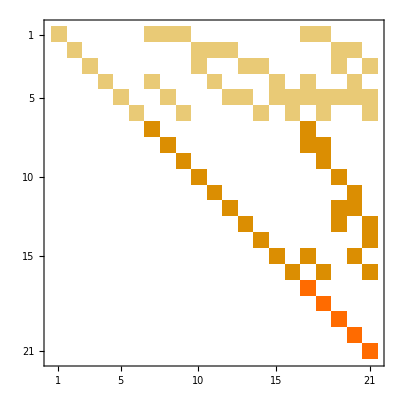

```mathematica
MatrixPlot[%528]
```

```mathematica
With[{g=MinimalGraph[6]},
Monitor[
MatrixForm[DropZeroRow[DropZeroCol[Total[
Table[
With[{form=Map[SymbolReplace[#,e]&,FindFullFormula[GContract[g,e]]]},
Print[form];
ZetaFunctionFromFormula[form]
],
{e,Map[SortEdge,EdgeList[GraphComplement[g]]]}

]
]]]
]
,
e]
]
```

{v1x2x35x4x6x7,v1x2x357x4x6,v1x2x35x47x6,v1x2x35x46x7,v1x2x357x46}

{v1x2x36x4x5x7,v1x2x36x4x57,v1x2x36x47x5}

{v1x2x37x4x5x6,v1x2x357x4x6,v1x2x37x46x5,v1x2x357x46}

{v1x2x3x46x5x7,v1x2x3x46x57,v1x2x37x46x5,v1x2x35x46x7,v1x2x357x46}

{v1x2x3x47x5x6,v1x2x36x47x5,v1x2x35x47x6}

{v1x2x3x4x57x6,v1x2x3x46x57,v1x2x357x4x6,v1x2x357x46,v1x2x36x4x57}

(1 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 1 | 0 | 0 | 0 | 0 | 1
0 | 1 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0
0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 0 | 1 | 0 | 1
0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 1
0 | 0 | 0 | 0 | 1 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1 | 1 | 0 | 0 | 0 | 1 | 0 | 1 | 1
0 | 0 | 0 | 0 | 0 | 0 | 3 | 0 | 0 | 0 | 0 | 0 | 0 | 3
0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 0 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 2 | 2
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 4)

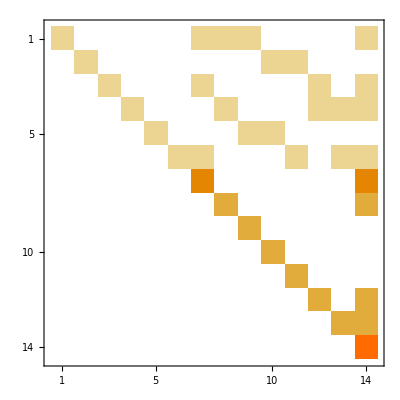

```mathematica
MatrixPlot[%531]
```